# Лабораторная работа №5

## Численное дифференцирование и интегрирование

Михалькевич Д.Н.
гр. 221701

Вариант 8

## Задание 1.

### Найти приближенные значения производных первого и второго порядков функции а) функцию D системы Mathematica;б) формулы численного дифференцирования...

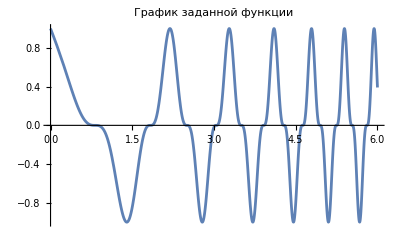

```mathematica
f[x_]:= (Cos[x^2+Sqrt[x]])^3;
Subscript[x, 0]=5.37;
initialPlot=Plot[f[x],{x, 0,6},PlotLabel -> "График заданной функции"];
Show[initialPlot]
```

#### а) функция D системы Mathematica

```mathematica
Print["Производная 1-го порядка: ", d1=D[f[x],x]/.x->Subscript[x, 0]]
Print["Производная 2-го порядка: ", d2=D[f[x],{x,2}]/.x->Subscript[x, 0] ]
```

Производная 1-го порядка: 7.93433

Производная 2-го порядка: -276.544

#### б) формулы численного дифференцирования

```mathematica
(* Функции конечных разностей 3 порядков*)
FDifference1[y_,y1_]:=y1-y; 
FDifference2[y_,y1_,y2_]:=y2-2y1+y;
FDifference3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
```

```mathematica
h=0.1; (* Для шага 0.1 *)
```

```mathematica
y1=1/h(FDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
y2=1/h^2(FDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: -10.17

Производная 2-го порядка: 110.009

Разница между вычисленными значениями 1-й производной: 18.1044

Разница между вычисленными значениями 2-й производной: 386.553

```mathematica
h=0.01; (* Для шага 0.01 *)
```

```mathematica
y1=1/h(FDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
y2=1/h^2(FDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: 8.0033

Производная 2-го порядка: -301.359

Разница между вычисленными значениями 1-й производной: 0.0689647

Разница между вычисленными значениями 2-й производной: 24.8149

Вывод: Уменьшение шага приводит к получению более точных результатов

## Задание 1.

### а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений производной функции на отрезке[-1, 3] с шагом h = 0,2.

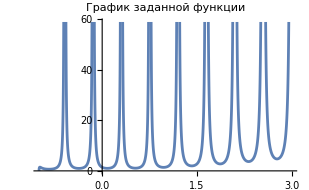

```mathematica
f[x_]:=(√(1+x^3))/Sin[7x+1]^2
Plot[f[x], {x,-1,3},PlotLabel -> "График заданной функции"]
```

```mathematica
a=-1;
b=3;
h=0.2;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{None,{"x_i","y'_i"}}]
```

x_i | y'_i
-1. | 1.76867-2.641 ⅈ
-0.8 | 649.616
-0.6 | 0.781656
-0.4 | -633.197
-0.2 | 0.98038
0. | -10.9183
0.2 | 3.35756
0.4 | -1.96918
0.6 | 24.7844
0.8 | 0.079858
1. | 6695.3
1.2 | 1.4152
1.4 | -6683.
1.6 | 3.82526
1.8 | -26.2419
2. | 12.1021
2.2 | -4.93659
2.4 | 70.4632
2.6 | -0.427103
2.8 | 168760.
3. | 2.54325

### б) Изобразить...

```mathematica
Derivate=D[f[x],x]
```

(3 x^2 Csc[1+7 x]^2)/(2 √(1+x^3))-14 √(1+x^3) Cot[1+7 x] Csc[1+7 x]^2

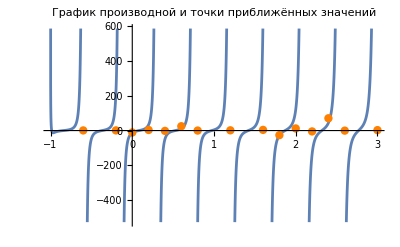

```mathematica
graph=Plot[Derivate,{x,-1,3}];
points=ListPlot[data,PlotStyle->{PointSize[0.015],Orange}];
Show[graph,points, PlotLabel-> "График производной и точки приближённых значений"]
```

## Задание 3

### Вычислить определенный интеграл: а) по формуле средних прямоугольников; б) по формуле трапеций.

```mathematica
f[x_]:=(√(2x+2.8))/(0.7 x^2+√(x^2+1.3))
a=0.8;
b=1.6;
Subscript[x, 0]=a;
```

```mathematica
n1=8;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

0.695637

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

0.695693

```mathematica
k=2;
Richardson=AverageRectangle2+n1^k/(n2^k-n1^k)(AverageRectangle2-AverageRectangle1)(*Уточнение по Ричардсону*)
```

0.695791

#### Б) Метод трапеций

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

0.696099

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

0.695988

```mathematica
Richardson=Trapezoidal2+n1^k/(n2^k-n1^k)(Trapezoidal2-Trapezoidal1)(*Уточнение по Ричардсону*)
```

0.695791

## Задание 4

### Вычислить определенный интеграл от таблично заданной функции по формуле Симпсона (парабол) для разбиений отрезка интегрирования на 8 и на 16 частей.

```mathematica
data=({{1.04, 0.9519}, {1.16, 0.8534}, {1.28, 0.7734}, {1.4, 0.7071}, {1.52, 0.6513}, {1.64, 0.6036}, {1.76, 0.5625}, {{{1.88}, {2}}, {{0.5265}, {0.4950}}}});
```

```mathematica
a=1.04;
b=2;
n=4;
h=(b-a)/(2n);
```

```mathematica
For[i=1,i<=2*n,i++, Subscript[y, i]=data[[i,2]];]
```

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

{{0.70252},{0.70126}}

#### Разбиение отрезка интегрирования на 16 частей

```mathematica
data=({{1.04, 0.9519}, {1.1, 0.9181}, {1.16, 0.8534}, {1.22, 0.8278}, {1.28, 0.7734}, {1.34, 0.7537}, {1.4, 0.7071}, {1.46, 0.6917}, {1.52, 0.6513}, {1.58, 0.6392}, {1.64, 0.6036}, {1.7, 0.5941}, {1.76, 0.5625}, {1.82, 0.5549}, {1.88, 0.5265}, {1.94, 0.5206}, {2, 0.4950}});
```

```mathematica
n=8;
h=(b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.656058

## Задание 5

### Вычислить определенный интеграл с помощью квадратурной формулы Гаусса с n узлами.

```mathematica
f[x_]=(3+Cos[x+2])/(x+2.4);
a=1.6;
b=3.2;
n=4;
polynomial = LegendreP[n,x]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
soluton=NSolve[polynomial==0,x];
xx=x/.soluton
```

{-0.861136,-0.339981,0.339981,0.861136}

```mathematica
T=Table[If[i==1,1,(xx[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.}

```mathematica
A=LinearSolve[T,B]
```

{0.347855,0.652145,0.652145,0.347855}

```mathematica
Integral=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*xx[[i]]]
```

0.903332